```mathematica
(* Nevanlinna rep stuff *)
```

```mathematica
disk2plane[z_]:= I (1 - z)/(1+z)
plane2disk[z_] := (1 + z I)/(1 - z I)
fixedFinder[f_, omega_]:= Module[{temp,fixedpoint},
temp=ReplaceAll[z,Solve[f[z, w]==z, z]]/.w->omega;
Select[temp, Abs[#]<1&, 1]]
rotNumberBand[f_, omega_]:= Module[{fp},
fp = fixedFinder[f, omega];
Arg[D[f[z, omega], z]/.z->fp]
]
```

```mathematica
(* this stuff is for testing the polynomial Subscript[Q, a] *)
```

```mathematica
reflect[p_, k_] := Module[{pflip},
pflip = Expand[w^k Conjugate[p[1/Conjugate[w]]]]
]
qa[a_, k_]:= (p1[w] - Exp[I a]reflect[p1, k])^2 + 4 Exp[I a] p2[w] reflect[p2, k]
```

```mathematica
(* Load up some graphs *)
```

```mathematica
n=5
AMatrices=AdjacencyMatrix/@(GraphData/@GraphData[n])//Normal;
```

5

## Graph generator

```mathematica
(* Random symmetric generator *)
preA = RandomInteger[{0,1}, {n,n}];
A = preA.Transpose[preA]
```

```mathematica
graphlist = {};
```

```mathematica
(* this loop generates all of the graphs and fixed point curves for associated functions - it takes a long time at n=6! *)
For[i=1,i<= First[Dimensions[AMatrices]],  i++,
A = AMatrices[[i]];
graph = AdjacencyGraph[A];
Y2 = {{1/2}};
Y1 =IdentityMatrix[n-1];
Y = ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold /@ {Y1, Y2}];
alpha = {1,0,0,0,0};
zY = z Y + (IdentityMatrix[n]-Y)w;
f[w_,z_]=-Simplify[plane2disk[((Inverse[A - zY].alpha).alpha/.{w->disk2plane[w], z->disk2plane[z]})]];
f[z,w]
Clear[g1, g2];
{g1[w_, c_]}= (z/.Solve[f[z,w]==  c,z]);
Clear[curve];
curve[z_]= w/.Solve[f[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All];
AppendTo[graphlist, {graph, fixed}];
]
```

Set::shape: Lists {g1[w_,c_]} and z are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

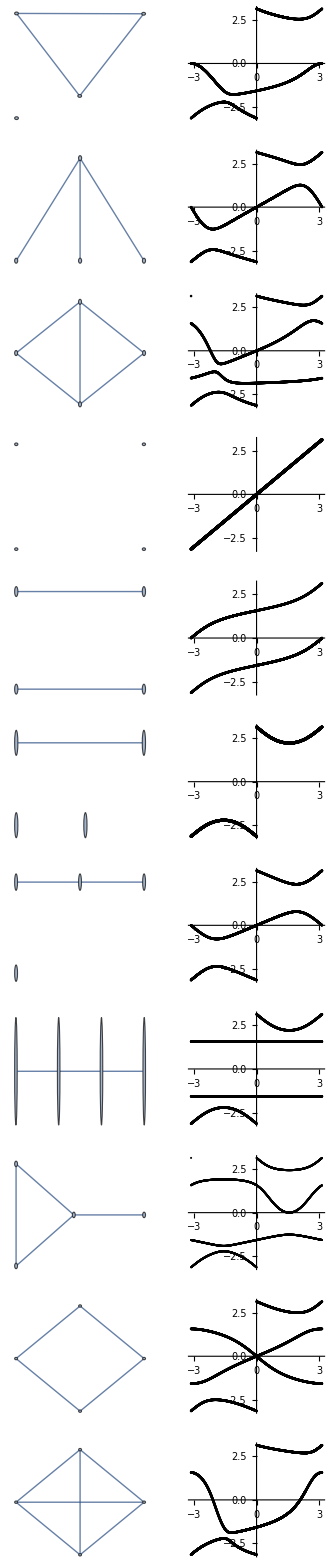

```mathematica
(* n=4 graphs and fixed points of resulting functions *)GraphicsGrid[graphlist]
```

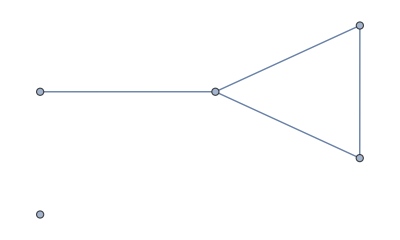
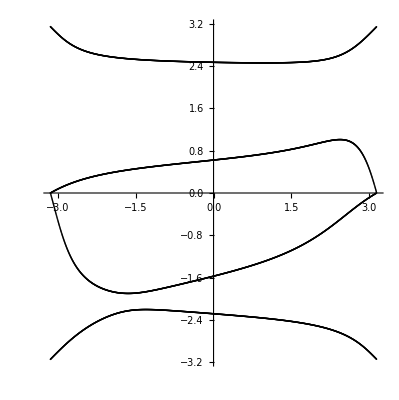
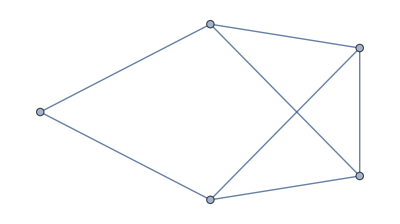
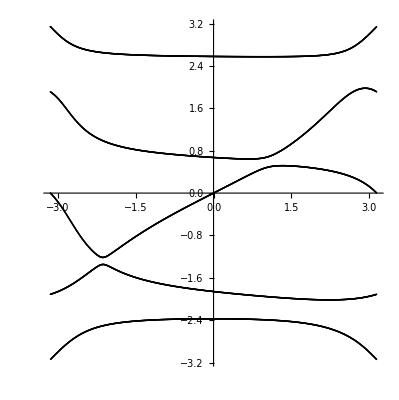
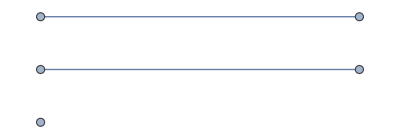
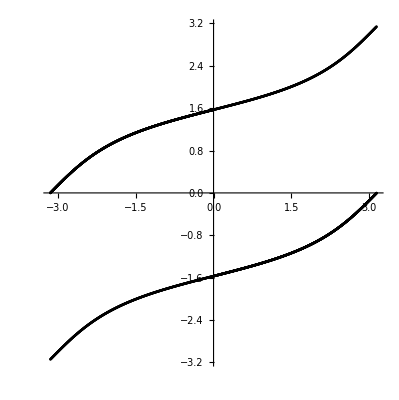
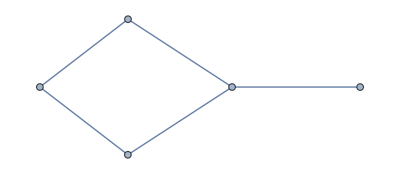
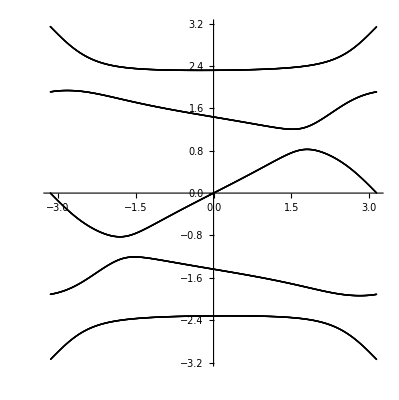
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
(*n = 5 *)
GraphicsGrid[graphlist]
```

## Test Individual Function

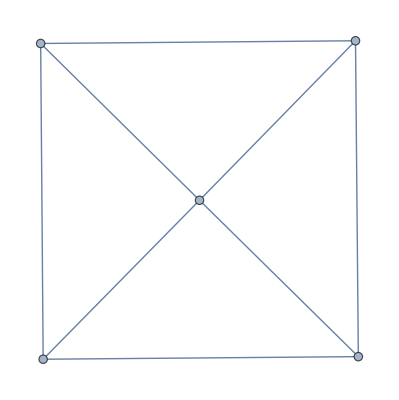

```mathematica
(*A = RandomChoice[AMatrices];*)
A = AMatrices[[34]];
graph = AdjacencyGraph[A]
```

```mathematica
Y2 = {{1/2}};
Y1 =IdentityMatrix[n-1];
Y = ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold /@ {Y1, Y2}];
alpha = {1,0,0,0,0}; (* adjust this to the correct dimension *)
zY = z Y + (IdentityMatrix[n]-Y)w;
f[w_,z_]=-Simplify[plane2disk[((Inverse[A - zY].alpha).alpha/.{w->disk2plane[w], z->disk2plane[z]})]];
```

-(((3-4 ⅈ)-10 w-(14-24 ⅈ) w^2-(2-32 ⅈ) w^3+(7+12 ⅈ) w^4+((1-4 ⅈ)-8 w-(4-24 ⅈ) w^2+(12+32 ⅈ) w^3+(15+12 ⅈ) w^4) z)/((15-12 ⅈ)+(12-32 ⅈ) w-(4+24 ⅈ) w^2-8 w^3+(1+4 ⅈ) w^4+((7-12 ⅈ)-(2+32 ⅈ) w-(14+24 ⅈ) w^2-10 w^3+(3+4 ⅈ) w^4) z))

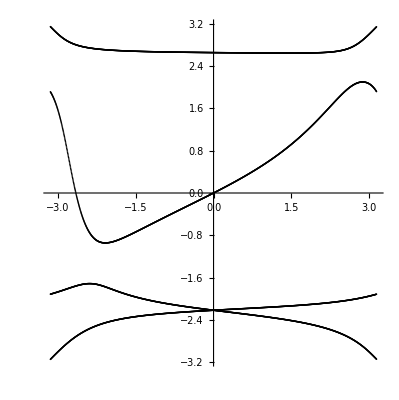

```mathematica
f[z,w]
Clear[g1];
{g1[w_, c_]}= (z/.Solve[f[z,w]==  c,z]);
Clear[curve];
curve[z_]= w/.Solve[f[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All];
Show[fixed]
```

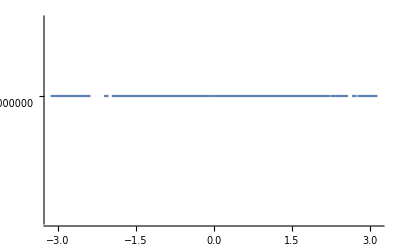

```mathematica
Plot[Abs[f[1, Exp[I t]]], {t, -Pi, Pi}]
```

```mathematica
Series[g1[z, t], {z,-1, 5}]//Simplify
```

-1-(z+1)-(z+1)^2+(z+1)^3+(((17-8 ⅈ)+(15-8 ⅈ) t) (z+1)^4)/(4+4 t)-(ⅈ ((52+19 ⅈ)+(96+22 ⅈ) t+(44+7 ⅈ) t^2) (z+1)^5)/(8 (1+t)^2)+O[z+1]^6

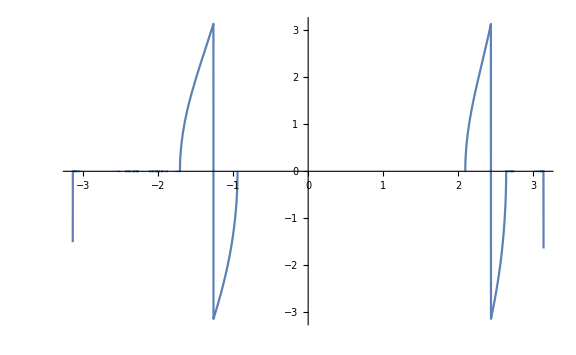

```mathematica
Plot[rotNumberBand[f, Exp[I s]], {s, -Pi, Pi}, ImageSize->Large, PlotPoints->100,PlotRange->{{-Pi,Pi},{-Pi, Pi}}]
```

```mathematica
p1[w_] := Coefficient[Denominator[f[z,w]], z, 0];
p2[w_]:= Coefficient[Denominator[f[z,w]], z, 1];
m = Exponent[Denominator[f[z,w]], w];
```

```mathematica
(*compute a *)
p1[-3/5 - 4/5 I]/p2[-3/5 - 4/5 I]
```

1+(8 ⅈ)/3

```mathematica
qa[Pi, m]//Factor
```

4 (5+6 w^2+5 w^4) (9-2 w^2+9 w^4)

This computation shows two double roots representing two normal crossings - in the arg plot, these correspond to the points (-1,-1) and (1, -3/5 - 4/5 I).

```mathematica
Roots[5+6 w+5 w^2==0,w]
```

w==-3/5-(4 ⅈ)/5||w==-3/5+(4 ⅈ)/5

```mathematica
FullSimplify[5+6 w+5 w^2]
```

5+w (6+5 w)

```mathematica
N[Arg[-3/5-(4 ⅈ)/5]]
```

-2.2143